# Mathematica Code for “Forecasting the impact of the viral ‘Kia Boys’ social media trend on car thefts to 2050”

## The following code reproduces: Figure 1, Figure 2, Figure 3A (excluding map), Figure 4, Figure 5, Figure 6 (excluding map), Figure 7, Figure 8, and Figure 9. Code Sections: Data: A code block that loads all of the needed data at once. Main Text Figures: Code reproducing each figure. Supplemental Movies: Code to reproduce the supplemental movies. Notes: Maps panels (Figure 3B) and Figure 6A were generated in Qgis and cannot be reproduced here. Figure 10 is reproduced in associated R code. Figure layout, including arrows and labeling, was completed in PowerPoint. These features are not reproduced in the code below. There is some redundancy in variable naming.

## Data

## Set Directory Path

```mathematica
pth="YOUR PATH TO REPOSITORY HERE";
```

## Data for Figure 1A and B

```mathematica
datFig1A1:=Import[pth<>"/data/tiktok-kia-boys.csv"]
```

```mathematica
datFig1A2:=Import[pth<>"/data/mainstream_dates.csv"]
```

## Data for Figure 2

```mathematica
datFig2ABC:=Import[pth<>"/data/multi-city-USAFactsShort-8-15-24.csv"]
```

## Data for Figure 3A

```mathematica
datFig3A:=Import[pth<>"/data/weekly_sonata_logistic-10-4-24.csv"]
```

## Data for Figure 4ABC (also used in Movies S1, S2 and S3)

```mathematica
datFig4A:=Import[pth<>"/data/sonata_thefts_by_year.csv"] (*combines with traffic data for Movie S1*)
```

```mathematica
datFig4B:=Import[pth<>"//data/civic_thefts_by_year.csv","Data"](*combines with traffic data for Movie S2*)
```

```mathematica
datFig4C:=Import[pth<>"/data/camry_thefts_by_year.csv"](*combines with traffic data for Movie S3*)
```

## Data for Figure 4DEF

```mathematica
datFig4D:=Import[pth<>"/data/model_sonata_final.csv"]
```

```mathematica
datFig4E:=Import[pth<>"/data/model_civic_final.csv"];
```

```mathematica
datFig4F:=Import[pth<>"/data/model_camry_final.csv"]
```

## Data for Figure 5ABC

```mathematica
datFig5A:=Import[pth<>"/data/forecast_final.csv"]
```

```mathematica
datwestFig5B=Import[pth<>"/data/forecast_west_final.csv"];
```

```mathematica
datsouthFig5C=Import[pth<>"/data/forecast_south_final.csv"];
```

## Data for Figure 6B

```mathematica
datFig6B=Import[pth<>"/data/west_south_income_2022_combined.csv"];
```

## Data for Figure 6CD

```mathematica
datFig6CD:=Import[pth<>"/data/civic_west_south_compare.csv","Data"]
```

## Data for Figure 7

```mathematica
datFig7=Import[pth<>"/data/sonta_civic_camry_sales_1973-2023.csv","Data"];
```

## Data for Figure 8A

```mathematica
datFig8A=Import[pth<>"/data/opitma_kia_boys_weekly.csv"];
```

## Data for Figure 8B

```mathematica
datFig8B:=Import[pth<>"/data/optima_thefts_by_year.csv"]
```

## Data for Figure 9

```mathematica
datFig9:=Import[pth<>"/data/optima_forecast_final.csv"]
```

## Data for Figure 10

```mathematica
datFig10A0:=Import[pth<>"/data/forecast_final.csv"]
datFig10A1:=Import[pth<>"/data/forecast_recall_2024.csv"]
datFig10A2:=Import[pth<>"/data/forecast_recall_2025.csv"]
datFig10A3:=Import[pth<>"/data/forecast_recall_2026.csv"]
```

```mathematica
ddatFig10A0=Drop[Drop[Drop[datFig10A0,None,{1}],None,{1,26}],1];
ddatFig10A1=Drop[Drop[Drop[datFig10A1,None,{1}],None,{1,26}],1];
ddatFig10A2=Drop[Drop[Drop[datFig10A2,None,{1}],None,{1,26}],1];
ddatFig10A3=Drop[Drop[Drop[datFig10A3,None,{1}],None,{1,26}],1];
```

```mathematica
tdatFig10A0=Total[ddatFig10A0];
tdatFig10A1=Total[ddatFig10A1];
tdatFig10A2=Total[ddatFig10A2];
tdatFig10A3=Total[ddatFig10A3];
```

## Data for Supplemental Movies

### Accident data combines with theft data from Figure 4 to produce supplemental movies

```mathematica
datS1:=Import[pth<>"/data/sonata_accidents_by_year.csv"]
```

```mathematica
datS2:=Import[pth<>"/data/civic_accidents_by_year.csv"]
```

```mathematica
datS3:=Import[pth<>"/data/camry_accidents_by_year.csv"]
```

### Note: Data for West and South Bureau movie is the same as for Figure 6

## Main Text Figures

## Figure 1A

### Figure 1A Code

```mathematica
ddatFig1A1=Drop[datFig1A1,1]; (*drop the row of headers*)
ddatFig1A2=Drop[datFig1A2,1]; (*drop the row of headers*)
```

```mathematica
vsdFig1A1=Flatten[Take[ddatFig1A1, All,{2}],1]; (*column with dates of events*)
vsdFig1A2=Flatten[Take[ddatFig1A2,All,{2}],1]; (*column with dates of events*)
```

```mathematica
vsdIFig1A1=Table[FromDateString[vsdFig1A1[[k]],{"Month","/","Day","/","YearShort"}],{k,1,Length[vsdFig1A1]}];  (*convert  dates into a useable format*)

vsdIFig1A2=Select[Table[FromDateString[vsdFig1A2[[k]],{"Month","/","Day","/","YearShort"}],{k,1,Length[vsdFig1A2]}],#<DateObject[{2023,12,1}]&]; (*convert dates into a useable format*)
```

### Figure 1A

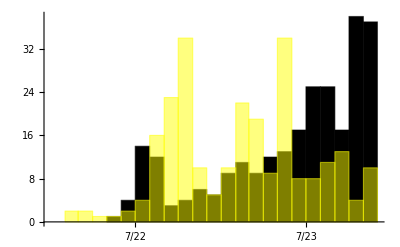

```mathematica
Fig1A=DateHistogram[{vsdIFig1A1,vsdIFig1A2,White},"Month",ChartStyle->{Directive[Opacity[1],Black],Yellow},LabelStyle->{(FontFamily->"Helvetica"),(FontSize->12)},PlotRange->{{DateObject[{2022,1,1}, "Month"],DateObject[{2023,12,15}, "Month"]},Automatic},DateTicksFormat->{"MonthShort","/","YearShort"}]
```

## Figure 1B

### Figure 1B Code

```mathematica
likesRawFig1B=Flatten[Take[ddatFig1A1, All,{9}],1]; (*column with tiktok likes count*)
```

```mathematica
(*data scrubbing to get the data into a form for a DateListPlot*)
```

```mathematica
stringToNumberWithSuffix[s_String]:=Module[{numString,suffix,number},{numString,suffix}=StringCases[s,(n:NumberString)~~(c:"K"|"M"|"B"|"T"|""):>{n,c}][[1]];
number=ToExpression[numString];
Switch[suffix,"K",number*1000,"M",number*1000000,"B",number*1000000000,"T",number*1000000000000,"",number,_,number (*default if no recognized suffix*)]]
```

```mathematica
likesFig1B={}; (*like numbers without suffixes*)
For[k=1,k<Length[likesRawFig1B]+1,k++,
AppendTo[likesFig1B,stringToNumberWithSuffix[likesRawFig1B[[k]]]];
]
```

```mathematica
likesKFig1B=N[likesFig1B/1000000]; (*convert to a number x * 10^6*)
```

```mathematica
vsdLikesFig1B=Partition[Riffle[vsdIFig1A1,likesKFig1B],2]; (*assemble into a bivariate structure*)
```

```mathematica
ts=TimeSeries[likesFig1B,{vsdIFig1A1}];(*convert into a timeseries object*)
```

```mathematica
vsdLGFig1B=GatherBy[vsdLikesFig1B,First];
```

```mathematica
dateLikesSumFig1B={};
For[i=1,i<Length[vsdLGFig1B]+1,i++,

localLen=Length[vsdLGFig1B[[i]]];
localSum=0;
For[j=1,j<localLen+1,j++,

localSum+=vsdLGFig1B[[i,j,2]];

];
AppendTo[dateLikesSumFig1B,{vsdLGFig1B[[i,1,1]],localSum}]

]
```

### Figure 1B

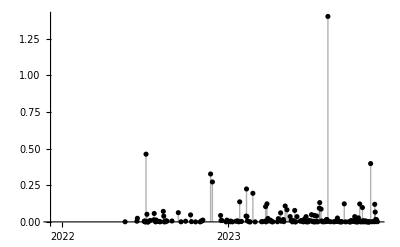

```mathematica
dateLikesSum2Fig1B=Prepend[dateLikesSumFig1B,{DateObject[{2021,12,6}],Null}];
ts2Fig1B=TimeSeries[dateLikesSum2Fig1B];
dlpFig1B=DateListPlot[ts2Fig1B,PlotRange->All,Filling->Axis,PlotStyle->Black,PlotRange->{{DateObject[{2022,7,1},"Day"],DateObject[{2023,12,30},"Day"]},Automatic},LabelStyle->{(FontFamily->"Helvetica"),(FontSize->12)},Joined->False,DateTicksFormat->{"MonthShort","/","YearShort"},Frame->False]
```

## Figure 2

### Figure 2 Code

```mathematica
ddatFig2ABC=Drop[datFig2ABC,1];(*drop the column names*)
```

```mathematica
headerFig2ABC=datFig2ABC[[1]];(*get the column names for chart labeling*)
```

```mathematica
sites=Take[headerFig2ABC,6;;11](*extract the specific names*)
```

{Albuquerque,Atlanta,Denver,Milwaukee,Seattle,Wichita}

```mathematica
ndatFig2ABC=Transpose[Take[ddatFig2ABC,All,{6,11}]];
```

```mathematica
tblsFig2ABC=Table[ListPlot[{ndatFig2ABC[[k]],{{18,0},{18,Max[DeleteMissing[ndatFig2ABC[[k]]]]+10}},{{40,0},{40,Max[DeleteMissing[ndatFig2ABC[[k]]]]+10}}},Joined->True,PlotLabel->sites[[k]],PlotStyle->{RGBColor["#00b0f0"],Red,{Red,Dashed}},LabelStyle->{FontFamily->"Helvetica",FontSize->18},PlotRange->{{0,50},{0,Max[DeleteMissing[ndatFig2ABC[[k]]]]+10}}],{k,1,6}];
```

### Figure 2

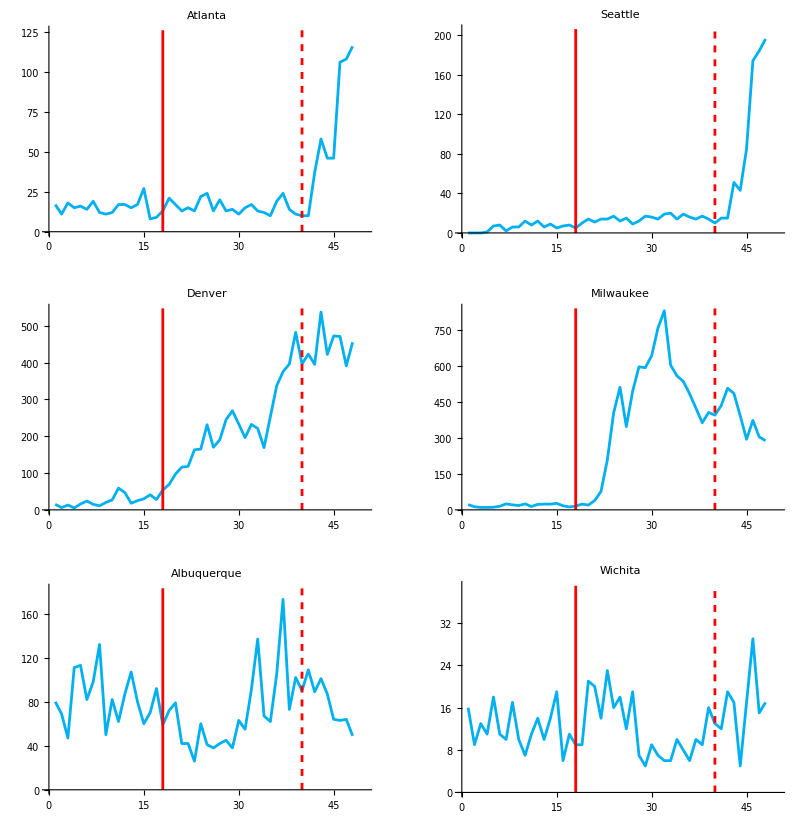

```mathematica
GraphicsGrid[{{tblsFig2ABC[[2]],tblsFig2ABC[[-2]]},{tblsFig2ABC[[3]],tblsFig2ABC[[4]]},{tblsFig2ABC[[1]],tblsFig2ABC[[-1]]}}]
```

## Figure 3A

### Figure 3A Code

```mathematica
ddatFig3A=Drop[datFig3A,1]; (*drop the column names*)
```

```mathematica
dateStringsFig3A=Table[FromDateString[ddatFig3A[[k,3]],{"Month","/","Day","/","YearShort"}],{k,1,Length[ddatFig3A]}];  (*convert the dates into a date object*)
```

```mathematica
wnumFig3A=Flatten[Take[ddatFig3A,All,{4}],1]; (*week number since week of Jan 1, 2017*)
mwnumFig3A = Min[wnumFig3A];  (*minimum week number*)
```

```mathematica
(*Sonata theft events*)
theftsFig3A=Flatten[Take[ddatFig3A,All,{5}],1];
tdatFig3A=Take[ddatFig3A,All,{4,5}];
mdatFig3A=Table[{tdatFig3A[[k,1]]-mwnumFig3A,tdatFig3A[[k,2]]},{k,1,Length[tdatFig3A]}]; (*week format*)
mdatFig3ADL=Table[{dateStringsFig3A[[k]],tdatFig3A[[k,2]]},{k,1,Length[tdatFig3A]}]; (*date object format*)
```

```mathematica
(*Kia Boys from USA Google*)
kbdatFig3A=Drop[Take[ddatFig3A,All,{4,6}],None,{2}];
m2datFig3A=Table[{kbdatFig3A[[k,1]]-mwnumFig3A,kbdatFig3A[[k,2]]},{k,1,Length[kbdatFig3A]}];
m2datFig3ADL=Table[{dateStringsFig3A[[k]],kbdatFig3A[[k,2]]},{k,1,Length[kbdatFig3A]}];
```

```mathematica
(*Kia Boys from Los Angeles YouTube*)
kbladatFig3A=Drop[Take[ddatFig3A,All,{4,7}],None,{2,3}];
m3datFig3A=Table[{kbladatFig3A[[k,1]]-mwnumFig3A,kbladatFig3A[[k,2]]},{k,1,Length[kbladatFig3A]}];
m3datFig3ADL=Table[{dateStringsFig3A[[k]],kbladatFig3A[[k,2]]},{k,1,Length[kbladatFig3A]}];
```

### Figure 3A

#### Note: Mathematica provides limited functionality for multi-axis display. The published figure was prepared in MS Excel. Here the theft and social media data are plotted with the same y-axis scaling.

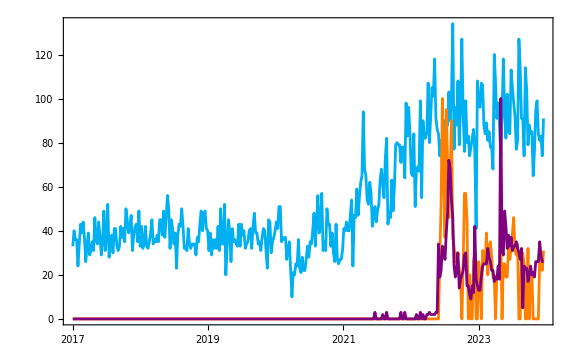

```mathematica
DateListPlot[{mdatFig3ADL,m3datFig3ADL,m2datFig3ADL}, Joined->True,PlotStyle->{RGBColor["#00b0f0"],Orange,Purple},LabelStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->Large,DateTicksFormat->{"MonthShort","/","YearShort"}]
```

```mathematica
(*Mean thefts per week 2017-2019*)
```

```mathematica
N[Mean[Flatten[Take[Select[mdatFig3ADL,#[[1]]<DateObject[{2020,1,1}]&],All,{2}],1]]]
```

37.6178

## Figure 4A

### Dates, Model Year and Theft Year “Ticks” for all Historical Data Matrix Plots

```mathematica
dates=Table[2000+i,{i,0,23}];
tyrtick=Table[{i+1,2000+i},{i,0,23,3}];
myeartick=Table[{i+1,1976+i},{i,0,47,5}];
```

### Figure 4A Code

```mathematica
ddatFig4A=ToExpression[Drop[datFig4A,1]]; (*drop the row of column names*)
```

```mathematica
gdatFig4A=Drop[ddatFig4A,None,{1}];(*drop the first column that marks these data as thefts = 1*)
```

```mathematica
mgdatFig4A=Drop[gdatFig4A[[1;;48]],None,{1}];(*drop the column of model-year dates*)
```

### Figure 4A

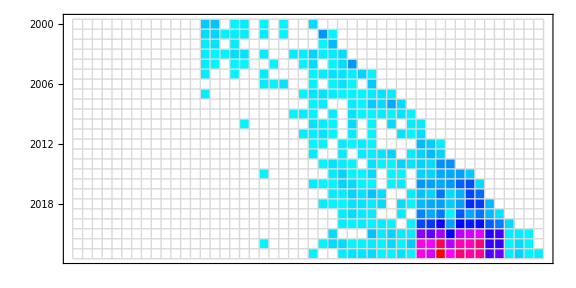

```mathematica
MatrixPlot[Transpose[mgdatFig4A],ColorFunction->(Hue[#]&),ColorRules->{0->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtick,None},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,16],FrameStyle->Directive[White]]
```

```mathematica
Max[mgdatFig4A] (*color scale bar max*)
```

322

## Figure 4B

### Figure 4B Code

```mathematica
ddatFig4B=ToExpression[Drop[datFig4B,1]]; (*drop the row of column names*)
```

```mathematica
gdatFig4B=Drop[ddatFig4B,None,{1}];(*drop the first column that marks these data as thefts = 1*)
```

```mathematica
mgdatFig4B=Drop[gdatFig4B[[1;;48]],None,{1}];(*drop the column of model-year dates*)
```

### Figure 4B

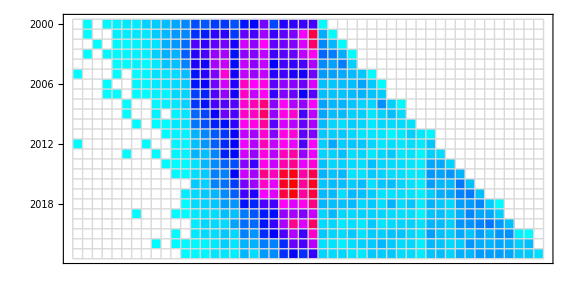

```mathematica
MatrixPlot[Transpose[mgdatFig4B],ColorFunction->(Hue[#]&),ColorRules->{0->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtick,None},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,16],FrameStyle->Directive[White]]
```

```mathematica
Max[mgdatFig4B](*color scale bar max*)
```

372

## Figure 4C

### Figure 4C Code

```mathematica
ddatFig4C=ToExpression[Drop[datFig4C,1]];
```

```mathematica
gdatFig4C=Drop[ddatFig4C,None,{1}];
```

```mathematica
mgdatFig4C=Drop[gdatFig4C[[1;;48]],None,{1}];
```

### Figure 4C

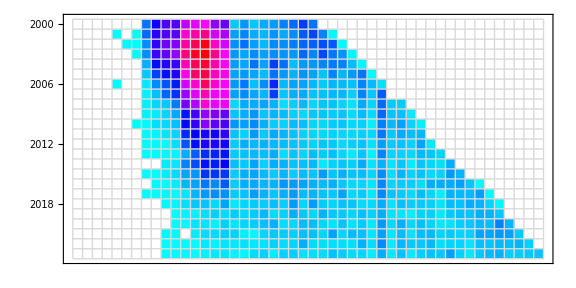

```mathematica
MatrixPlot[Transpose[mgdatFig4C],ColorFunction->(Hue[#]&),ColorRules->{0->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtick,None},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,16],FrameStyle->Directive[White]]
```

```mathematica
Max[mgdatFig4C](*color scale bar max*)
```

786

## Figure 4D

### Figure 4D Code

```mathematica
ddatFig4D=Drop[Drop[datFig4D,1],None,{1}]; (*drop the first column and the first row of column names*)
```

### Figure 4D

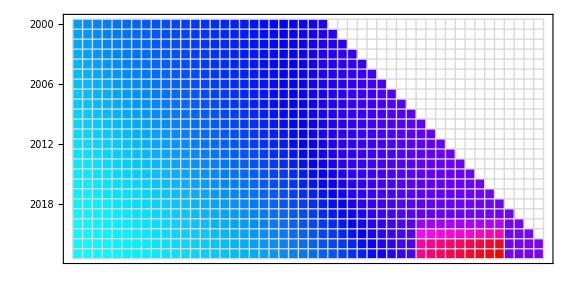

```mathematica
mpFig4D =MatrixPlot[Transpose[ddatFig4D],ColorFunction->(Hue[#]&),ColorRules->{0.->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtick,None},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,16],FrameStyle->Directive[White]]
```

```mathematica
Max[ddatFig4D](*color scale bar max*)
```

236.896

## Figure 4E

### Figure 4D Code

```mathematica
ddatFig4E=Drop[Drop[datFig4E,1],None,{1}];(*drop the first column and the first row of column names*)
```

### Figure 4E

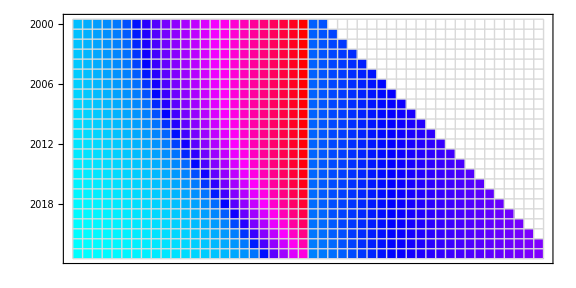

```mathematica
mpFig4E =MatrixPlot[Transpose[ddatFig4E],ColorFunction->(Hue[#]&),ColorRules->{0.->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtick,None},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,16],FrameStyle->Directive[White]]
```

```mathematica
Max[ddatFig4E](*color scale bar max*)
```

208.803

## Figure 4F

### Figure 4D Code

```mathematica
ddatFig4F=Drop[Drop[datFig4F,1],None,{1}];(*drop the first column and the first row of column names*)
```

### Figure 4D

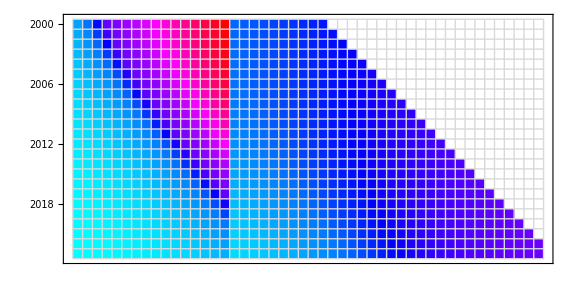

```mathematica
mpFig4F =MatrixPlot[Transpose[ddatFig4F],ColorFunction->(Hue[#]&),ColorRules->{0.->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtick,None},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,16],FrameStyle->Directive[White]]
```

```mathematica
Max[ddatFig4F](*color scale bar max*)
```

535.913

## Figure 5A

### Figure 5A Code

```mathematica
ddatFig5A=Drop[datFig5A,1];
```

```mathematica
(*fdatFig5A=Take[ddatFig5A,{r2019,r2020},{p2018,p2049}];*)
fdatFig5A=Take[ddatFig5A,{44,45},{20,51}];
```

```mathematica
diff1Fig5A=Reverse[Table[fdatFig5A[[1,k]]-fdatFig5A[[2,k]],{k,1,Length[fdatFig5A[[1]]]}]];
```

```mathematica
tdat1Fig5A=Take[ddatFig5A,All,{20,51}];
```

```mathematica
(*tdatFig5A=Take[tdat1,{r2007,r2023},All];*)
tdatFig5A=Take[tdat1Fig5A,{32,48},All];
```

```mathematica
tyrtickFig5A=Table[{i+1,2018+i},{i,0,30,3}];
myeartickFig5A=Table[{i+1,2007+i},{i,0,17,5}];
```

### Figure 5A

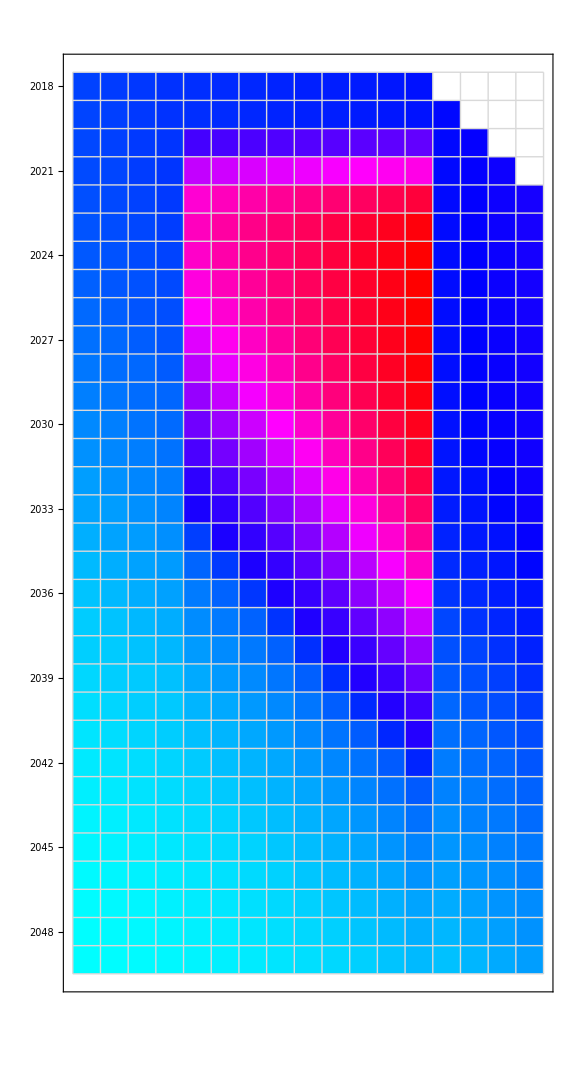

```mathematica
mpFig5A =MatrixPlot[Transpose[tdatFig5A],ColorFunction->(Hue[#]&),ColorRules->{0.->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtickFig5A,None},{None,myeartickFig5A}},ImageSize->Large,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[White]]
```

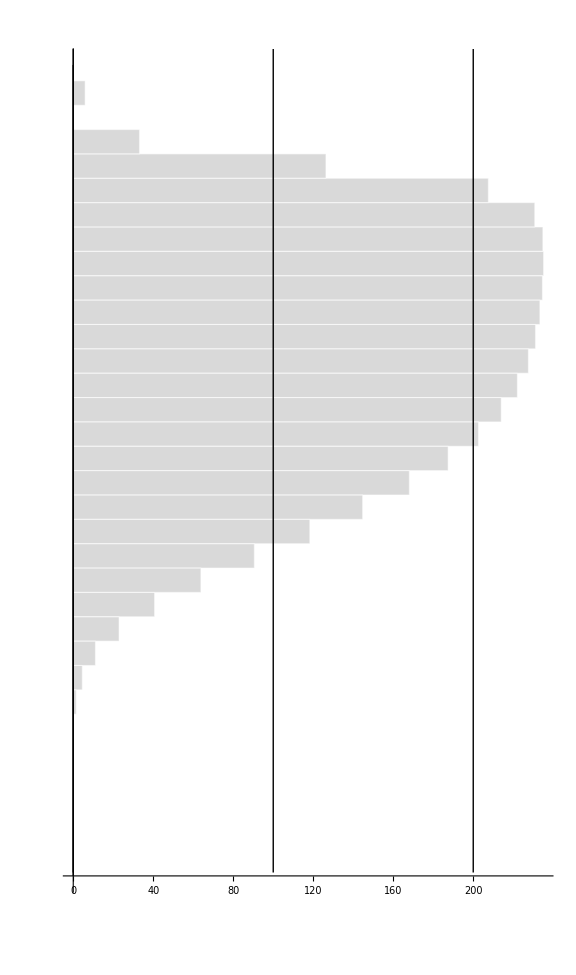

```mathematica
BarChart[diff1Fig5A, BarOrigin->Left, AspectRatio->(144/85),ImageSize->Large, ChartStyle->{Directive[LightGray,EdgeForm[White],EdgeForm[Thick]]},AxesOrigin->{Automatic, Automatic},BarSpacing->None, Epilog->{{Black,Thick,Line[{{0,0},{0,50}}]},{Black,Thick,Line[{{100,0},{100,50}}]},{Black,Thick,Line[{{200,0},{200,50}}]}}]
```

## Figure 5B

### Figure 5B Code

```mathematica
ddatwestFig5B=Drop[Drop[datwestFig5B,1],None,{1}];
```

```mathematica
tyrtickFig5B=Table[{i+1,2018+i},{i,0,30,3}];
myeartickFig5B=Table[{i+1,2007+i},{i,0,17,5}];
```

### Figure 5B

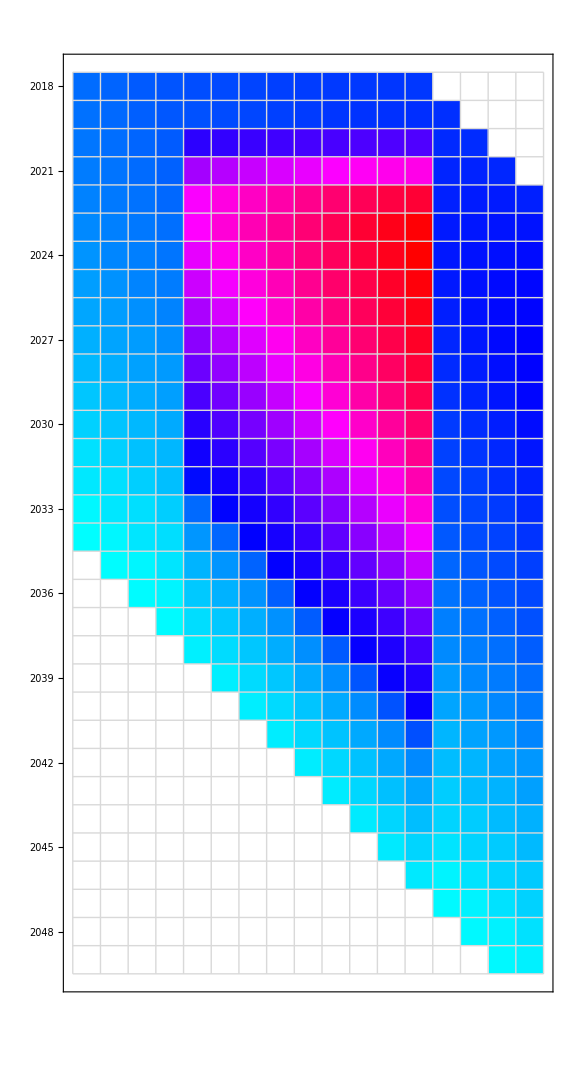

```mathematica
MatrixPlot[Transpose[ddatwestFig5B[[32;;48,19;;50]]],ColorFunction->(Hue[#]&),ColorRules->{0.->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtickFig5B,None},{None,myeartickFig5B}},ImageSize->Large,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[White]]
```

```mathematica
Max[ddatwestFig5B[[32;;48,19;;50]]]
```

65.5596

```mathematica
fwdatFig5B=Take[ddatwestFig5B,{44,45},{19,50}];
```

```mathematica
wdiff1Fig5B=Reverse[Table[fwdatFig5B[[1,k]]-fwdatFig5B[[2,k]],{k,1,Length[fwdatFig5B[[1]]]}]];
```

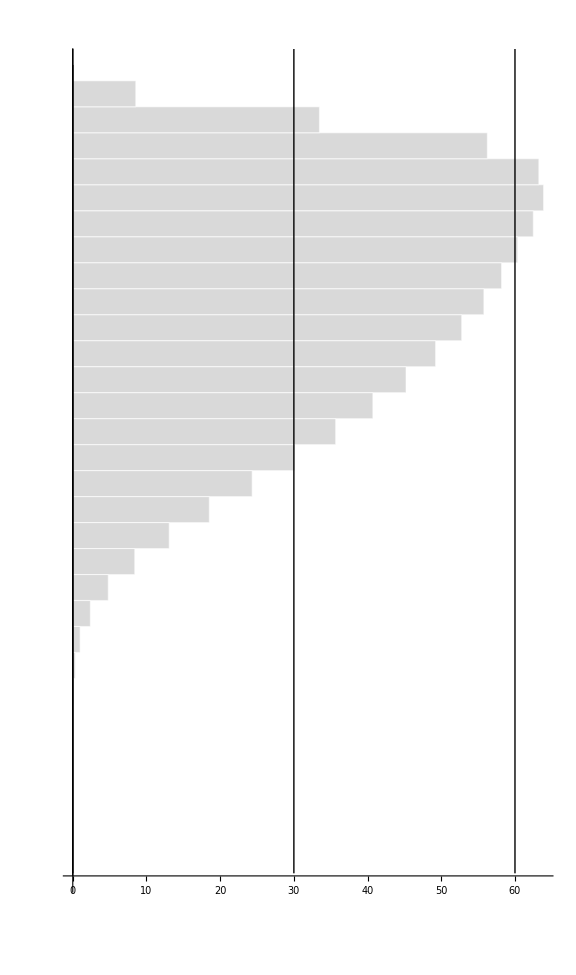

```mathematica
BarChart[wdiff1Fig5B[[1;;-3]], BarOrigin->Left, AspectRatio->(144/85),ImageSize->Large, ChartStyle->{Directive[LightGray,EdgeForm[White],EdgeForm[Thick]]},AxesOrigin->{Automatic, Automatic},BarSpacing->None,Epilog->{{Black,Thick,Line[{{0,0},{0,50}}]},{Black,Thick,Line[{{30,0},{30,50}}]},{Black,Thick,Line[{{60,0},{60,50}}]}}]
```

## Figure 5C

### Figure 5C Code

```mathematica
ddatsouthFig5C=Drop[Drop[datsouthFig5C,1],None,{1}];
```

```mathematica
tyrtickFig5C=Table[{i+1,2018+i},{i,0,30,3}];
myeartickFig5C=Table[{i+1,2007+i},{i,0,17,5}];
```

### Figure 5C

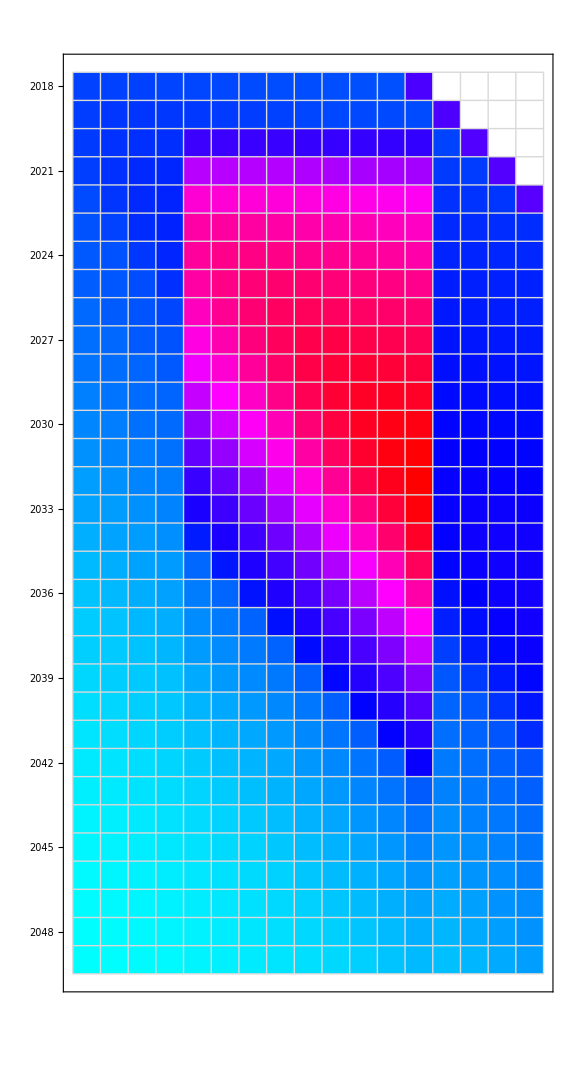

```mathematica
MatrixPlot[Transpose[ddatsouthFig5C[[32;;48,19;;50]]],ColorFunction->(Hue[#]&),ColorRules->{0.->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtickFig5C,None},{None,myeartickFig5C}},ImageSize->Large,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[White]]
```

```mathematica
Max[ddatsouthFig5C[[32;;48,19;;50]]]
```

46.8509

```mathematica
fsdatFig5C=Take[ddatsouthFig5C,{44,45},{19,50}];
```

```mathematica
sdiff1Fig5C=Reverse[Table[fsdatFig5C[[1,k]]-fsdatFig5C[[2,k]],{k,1,Length[fsdatFig5C[[1]]]}]];
```

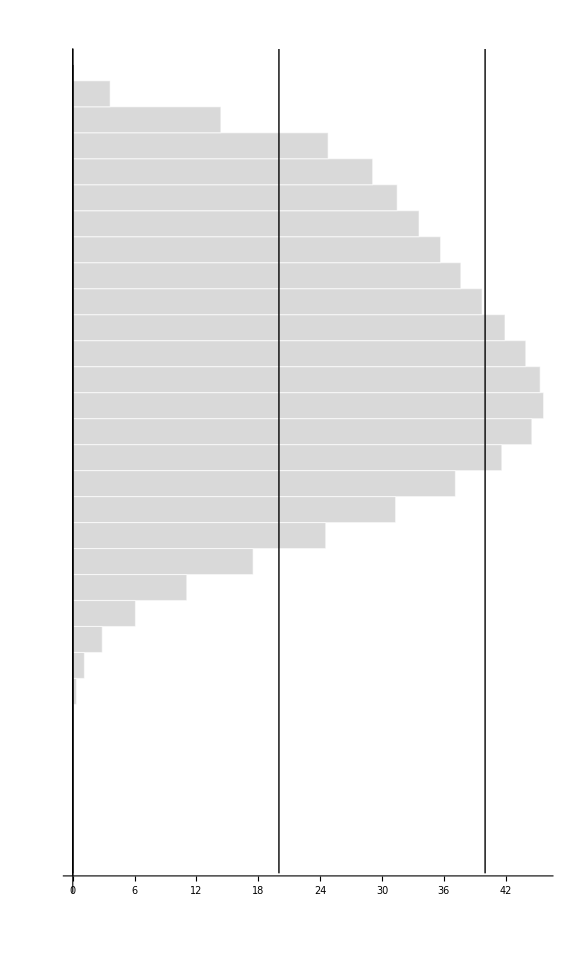

```mathematica
BarChart[sdiff1Fig5C[[1;;-3]], BarOrigin->Left, AspectRatio->(144/85),ImageSize->Large, ChartStyle->{Directive[LightGray,EdgeForm[White],EdgeForm[Thick]]},AxesOrigin->{Automatic, Automatic},BarSpacing->None,Epilog->{{Black,Thick,Line[{{0,0},{0,50}}]},{Black,Thick,Line[{{20,0},{20,50}}]},{Black,Thick,Line[{{40,0},{40,50}}]}}]
```

## Figure 6B

### Figure 6B Code

```mathematica
ddatFig6B=Select[Drop[datFig6B,1],#[[4]]>4&];(*drop missing values*)
```

```mathematica
gdatFig6B=GatherBy[ddatFig6B,#[[2]]&];(*group by bureau*)
```

```mathematica
wdatFig6B=Flatten[Take[gdatFig6B[[2]],All,{-1}]];(*isolate the west bureau data*)
sdatFig6B=Flatten[Take[gdatFig6B[[1]],All,{-1}]];(*isolate the south bureau data*)
```

### Figure 6B

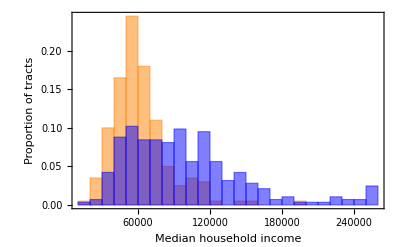

```mathematica
Histogram[{sdatFig6B,wdatFig6B},{10000},"Probability",ChartStyle->{Orange,Blue},Frame->True,FrameLabel->{"Median household income","Proportion of tracts"}]
```

## Figure 6CD

### Figure 6CD Code

```mathematica
ddatFig6CD=ToExpression[Drop[datFig6CD,1]];(*the 2023 version of mathematica need to convert from string*)
```

```mathematica
grdatFig6CD=GroupBy[ddatFig6CD,First];
```

```mathematica
gdatFig6CD=Drop[grdatFig6CD[[1]],None,{1}];(*this is all the civic data city-wide*)
wdatFig6CD=Drop[grdatFig6CD[[2]],None,{1}]; (*west bureau only*)
sdatFig6CD=Drop[grdatFig6CD[[3]],None,{1}]; (*south bureau only*)
```

```mathematica
mwdatFig6CD=Drop[wdatFig6CD[[1;;48]],None,{1}];
```

```mathematica
msdatFig6CD=Drop[sdatFig6CD[[1;;48]],None,{1}];
```

### Figure 6C

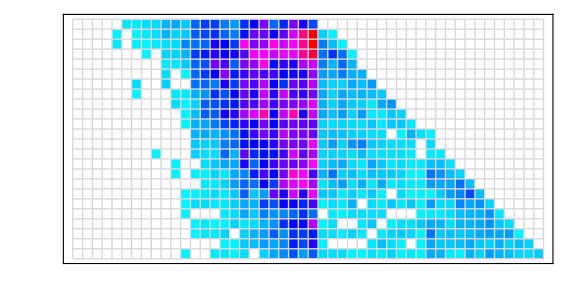

```mathematica
MatrixPlot[Transpose[mwdatFig6CD],ColorFunction->(Hue[#]&),ColorRules->{0->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{None,tyrtick},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[White]]
```

```mathematica
Max[Flatten[mwdatFig6CD]](*color scale bar max*)
```

94

### Figure 6D

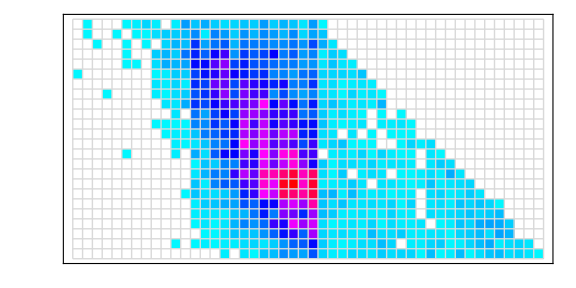

```mathematica
MatrixPlot[Transpose[msdatFig6CD],ColorFunction->(Hue[#]&),ColorRules->{0->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{None,tyrtick},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[White]]
```

```mathematica
Max[Flatten[msdatFig6CD]](*color scale bar max*)
```

114

## Figure 7

### Figure 7 Code

```mathematica
ddatFig7=Drop[datFig7,1];(*drop column names*)
```

```mathematica
sonDatFig7=Drop[ddatFig7,None,{2,3}];(*get the sonata data*)
civDatFig7=Drop[Drop[ddatFig7,None,{-1}],None,{2}];(*get the civic data*)
camDatFig7=Drop[ddatFig7,None,{3,4}];(*get the camry data*)
```

### Figure 7

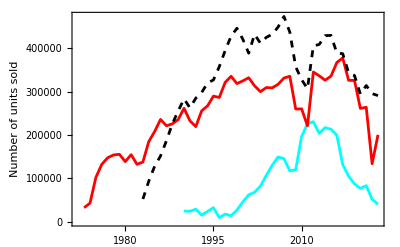

```mathematica
ListLinePlot[{sonDatFig7,civDatFig7,camDatFig7},Frame->True,PlotStyle->{Cyan,Red,{Black,Dashed}},FrameLabel->{"","Number of units sold"}]
```

## Figure 8A

### Figure 8A Code

```mathematica
ddatFig8A=Drop[datFig8A,1]; (*drop the column names*)
```

```mathematica
dateStringsFig8A=Table[FromDateString[ddatFig8A[[k,1]],{"Month","/","Day","/","YearShort"}],{k,1,Length[ddatFig8A]}];  (*convert the dates into a date object*)
```

```mathematica
(*Optima theft events*)
theftsFig8A=Flatten[Take[ddatFig8A,All,{3}],1]; (*column with thefts*)
mdatFig8ADL=Table[{dateStringsFig8A[[k]],tdatFig8A[[k,2]]},{k,1,Length[tdatFig8A]}]; (*date object format*)
```

```mathematica
(*Kia Boys from USA Google*)
kbdatFig8A=Drop[Take[ddatFig8A,All,{2,4}],None,{2}];
m2datFig8ADL=Table[{dateStringsFig8A[[k]],kbdatFig8A[[k,2]]},{k,1,Length[kbdatFig8A]}];
```

### Figure 8A

#### Note: Mathematica provides limited functionality for multi-axis display. The published figure was prepared in MS Excel. Here the theft and social media data are plotted with the same y-axis scaling.

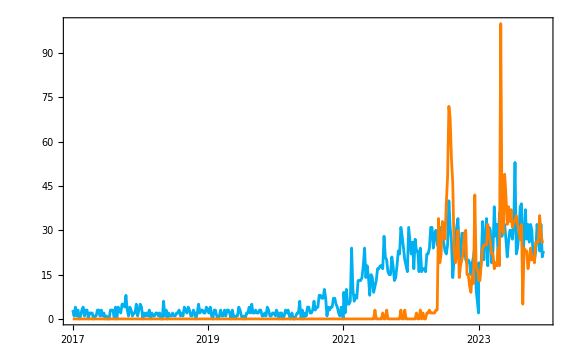

```mathematica
DateListPlot[{mdatFig8ADL,m2datFig8ADL}, Joined->True,PlotStyle->{RGBColor["#00b0f0"],Orange,Purple},LabelStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->Large,DateTicksFormat->{"MonthShort","/","YearShort"},PlotRange->Full]
```

## Figure 8B

### Figure 8B Code

```mathematica
ddatFig8B=Drop[datFig8B,1];
```

```mathematica
gdatFig8B=Drop[ddatFig8B,None,{1,2}];
```

```mathematica
mgdatFig8B=Drop[gdatFig8B[[1;;48]],None,{1}];
```

### Figure 8B

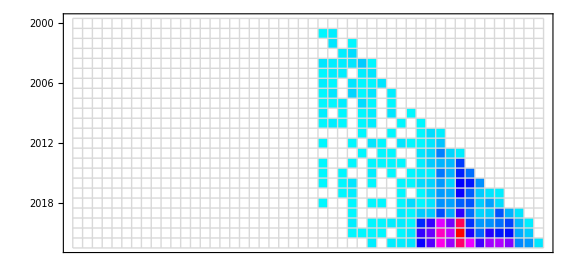

```mathematica
MatrixPlot[Transpose[mgdatFig8B],ColorFunction->(Hue[#]&),ColorRules->{0->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtick,None},{None,myeartick}},ImageSize->Large,FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[White]]
```

## Figure 9

### Figure 9 Code

```mathematica
headerFig9=Flatten[Take[datFig9,1],1];(*get the column names*)
p2018Fig9= Position[headerFig9,2018.][[1,1]];(*find the position of dates values in column names*)
p2049Fig9= Position[headerFig9,2049.][[1,1]];(*find the position of dates values in column names*)
```

```mathematica
p2018Fig9
```

20

```mathematica
ddatFig9=Drop[datFig9,1];(*drop the column names*)
```

```mathematica
rowerFig9=Flatten[Take[ddatFig9,All,{1}]];
r2007Fig9=Position[rowerFig9,2007][[1,1]];(*find the position of dates values in row labels names*)
r2023Fig9=Position[rowerFig9,2023][[1,1]];(*find the position of dates values in row labels names*)
r2020Fig9=Position[rowerFig9,2020][[1,1]];(*find the position of dates values in row labels names*)
r2021Fig9=Position[rowerFig9,2021][[1,1]];(*find the position of dates values in row labels names*)
```

```mathematica
fdatFig9=Take[ddatFig9,{r2020Fig9,r2021Fig9},{p2018Fig9,p2049Fig9}];(*extract the relevant rows and columns*)
```

```mathematica
diff1Fig9=Reverse[Table[fdatFig9[[1,k]]-fdatFig9[[2,k]],{k,1,Length[fdatFig9[[1]]]}]];(*the the difference between 2020 and 2021 years*)
```

```mathematica
tdat1Fig9=Take[ddatFig9,All,{p2018Fig9,p2049Fig9}];
tdatFig9=Take[tdat1Fig9,{r2007Fig9,r2023Fig9},All];
```

```mathematica
tyrtickFig9=Table[{i+1,2018+i},{i,0,30,3}];(*tick values for matrix plot*)
myeartickFig9=Table[{i+1,2007+i},{i,0,17,5}];
```

### Figure 9 Matrix Plot

9 Figure Matrix Plot

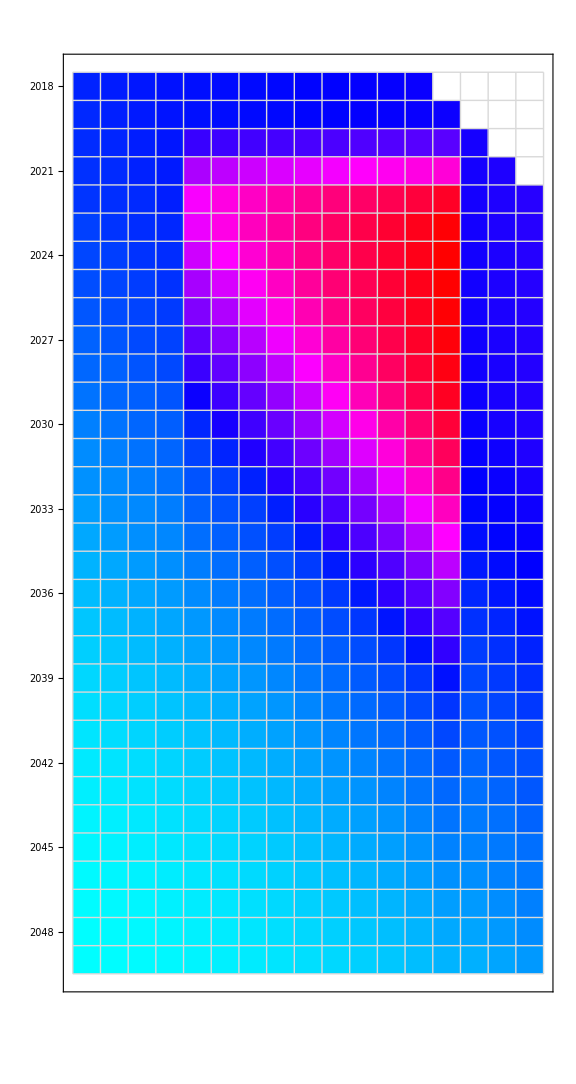

```mathematica
MatrixPlot[Transpose[tdatFig9],ColorFunction->(Hue[#]&),ColorRules->{0.->White},Mesh->All,MeshStyle->LightGray,FrameTicks->{{tyrtickFig9,None},{None,myeartickFig9}},ImageSize->Large,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[White]]
```

```mathematica
Max[ddatFig9[[32;;48,19;;50]]](*color scale maximum*)
```

201.182

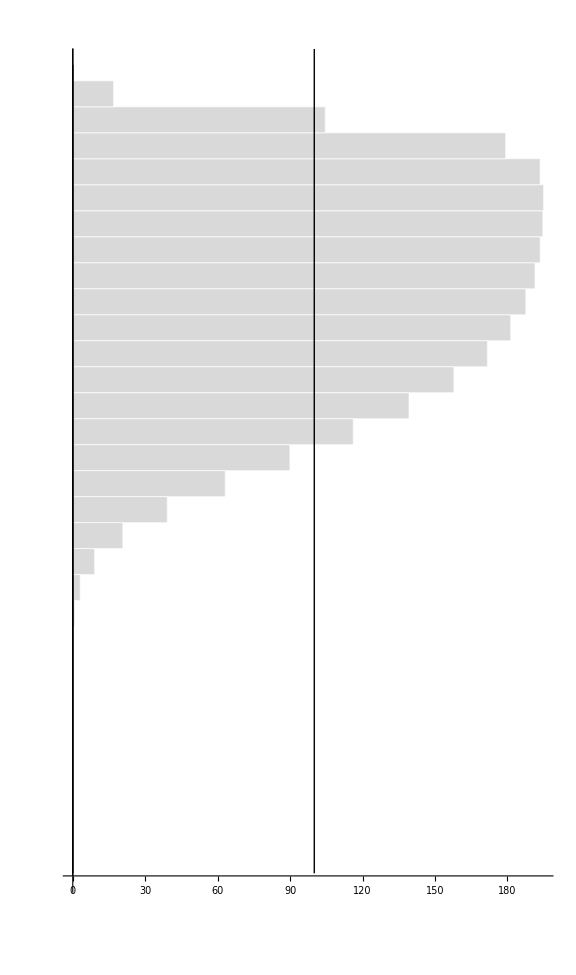

```mathematica
BarChart[diff1Fig9[[1;;-3]], BarOrigin->Left, AspectRatio->(144/85),ImageSize->Large, ChartStyle->{Directive[LightGray,EdgeForm[White],EdgeForm[Thick]]},AxesOrigin->{Automatic, Automatic},BarSpacing->None,Epilog->{{Black,Thick,Line[{{0,0},{0,50}}]},{Black,Thick,Line[{{100,0},{100,50}}]},{Black,Thick,Line[{{200,0},{200,50}}]}}]
```

## Figure 10AB

### Figure 10 Code

```mathematica
(*NHTSA recall completion rate model (Eq.8 in paper); Parameters from NHTSA 2021 report,Fig.10,for Hyundai Sonata*)
```

```mathematica
L1Fig10A=100.51111786; 
k1Fig10A=-0.22285628;
x01Fig10A=7.9678379;
C1Fig10A=-0.26576496;
```

```mathematica
fFig10A[L1Fig10A_,k1Fig10A_,x01Fig10A_,C1Fig10A_,x_]:=C1Fig10A+(L1Fig10A-C1Fig10A)/(1+Exp[-k1Fig10A*(x-x01Fig10A)]);
```

### Figure 10A

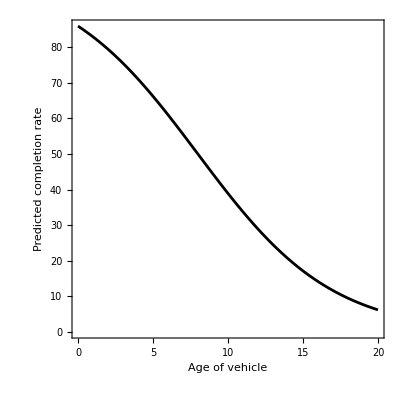

```mathematica
Plot[fFig10A[L1Fig10A,k1Fig10A,x01Fig10A,C1Fig10A,x],{x,0,20},PlotStyle->Black,AspectRatio->1,Frame->True,FrameLabel->{"Age of vehicle","Predicted completion rate"}]
```

### Figure 10B

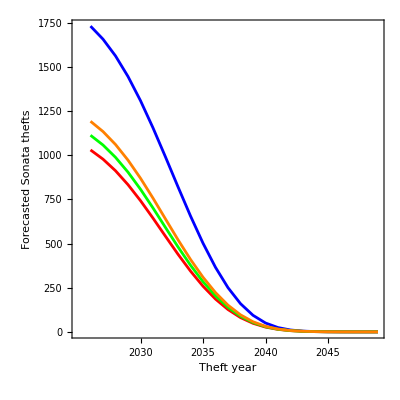

```mathematica
ListPlot[{tdatFig10A0,tdatFig10A1,tdatFig10A2,tdatFig10A3},Joined->True,PlotStyle->{Blue,Red,Green,Orange},AspectRatio->1,FrameTicks->{{{5,2030},{10,2035},{15,2040},{20,2045}},Automatic},Frame->True,FrameLabel->{"Theft year","Forecasted Sonata thefts"}]
```

## Supplemental Movies

## Movie S1

### Movie S1 Code

```mathematica
ddatS1=ToExpression[Drop[Drop[datS1,None,{1}],1]];
```

```mathematica
tbl3pMovieS1data=Table[ListPlot[{Partition[Riffle[Flatten[Take[ddatS1,All,{1}],1],Flatten[Take[ddatS1,All,{k}],1]],2],Partition[Riffle[Flatten[Take[gdatFig4A,All,{1}],1],Flatten[Take[gdatFig4A,All,{k}],1]],2]},Joined->True,PlotRange->{{1975,2023},{0,350}},Ticks->{{1980,2000,2020},{0,100,200,300}},AxesLabel->{Style["m",Medium,Black],Style["n",Medium,Black]},LabelStyle->{{FontSize->18,Black}},PlotLabel->dates[[k-1]],PlotStyle->{Red,Black},PlotLegends->Placed[LineLegend[{"accidents","thefts"},LegendLabel->"Hyundai Sonata"],After]],{k,2,25}];
```

### Movie S1

```mathematica
ResourceFunction["SimpleListAnimate"][tbl3pMovieS1data,AnimationRate->1,FrameMargins->None,Frame->None]
```

## Movie S2

### Movie S2 Code

```mathematica
ddatS2=ToExpression[Drop[Drop[datS2,None,{1}],1]];
```

```mathematica
tbl3LargeFig4B=Table[ListPlot[{Partition[Riffle[Flatten[Take[ddatS2,All,{1}],1],Flatten[Take[ddatS2,All,{k}],1]],2],Partition[Riffle[Flatten[Take[gdatFig4B,All,{1}],1],Flatten[Take[gdatFig4B,All,{k}],1]],2]},Joined->True,PlotRange->{{1975,2023},{0,550}},Ticks->{{1980,2000,2020},{0,100,200,300,400,500}},AxesLabel->{Style["m",Medium,Black],Style["n",Medium,Black]},LabelStyle->{{FontSize->18,Black}},PlotLabel->dates[[k-1]],PlotStyle->{Red,Black},PlotLegends->Placed[LineLegend[{"accidents","thefts"},LegendLabel->"Honda Civic"],After]],{k,2,25}];
```

### Movie S2

```mathematica
ResourceFunction["SimpleListAnimate"][tbl3LargeFig4B,AnimationRate->1,FrameMargins->None,Frame->None]
```

## Movie S3

### Movie S3 Code

```mathematica
ddatS3=ToExpression[Drop[Drop[datS3,None,{1}],1]];
```

```mathematica
tbl3LargeFig4C=Table[ListPlot[{Partition[Riffle[Flatten[Take[ddatS3,All,{1}],1],Flatten[Take[ddatS3,All,{k}],1]],2],Partition[Riffle[Flatten[Take[gdatFig4C,All,{1}],1],Flatten[Take[gdatFig4C,All,{k}],1]],2]},Joined->True,PlotRange->{{1975,2023},{0,800}},Ticks->{{1980,2000,2020},{0,200,400,600,800}},AxesLabel->{Style["m",Medium,Black],Style["n",Medium,Black]},LabelStyle->{{FontSize->18,Black}},PlotLabel->dates[[k-1]],PlotStyle->{Red,Black},PlotLegends->Placed[LineLegend[{"accidents","thefts"},LegendLabel->"Toyota Camry"],After]],{k,2,25}];
```

### Movie S3

```mathematica
ResourceFunction["SimpleListAnimate"][tbl3LargeFig4C,AnimationRate->1,FrameMargins->None,Frame->None]
```

## Movie S4

### Movie S4 Code

```mathematica
tbl3LargeFig6CD=Table[ListPlot[{Partition[Riffle[Flatten[Take[wdatFig6CD,All,{1}],1],Flatten[Take[wdatFig6CD,All,{k}],1]],2],Partition[Riffle[Flatten[Take[sdatFig6CD,All,{1}],1],Flatten[Take[sdatFig6CD,All,{k}],1]],2]},Joined->True,PlotRange->{{1975,2025},{0,150}},Ticks->{{1980,2000,2020},{0,50,100,150}},AxesLabel->{Style["m",Medium,Black],Style["n",Medium,Black]},LabelStyle->{{FontSize->18}},PlotLabel->dates[[k-1]],PlotStyle->{Orange,Blue},PlotLegends->Placed[LineLegend[{"West","South"},LegendLabel->"Honda Civic"],After]],{k,2,25}];
```

### Movie S4

```mathematica
ResourceFunction["SimpleListAnimate"][tbl3LargeFig6CD,AnimationRate->1,FrameMargins->None,Frame->None]
```